59867.7

76543.9

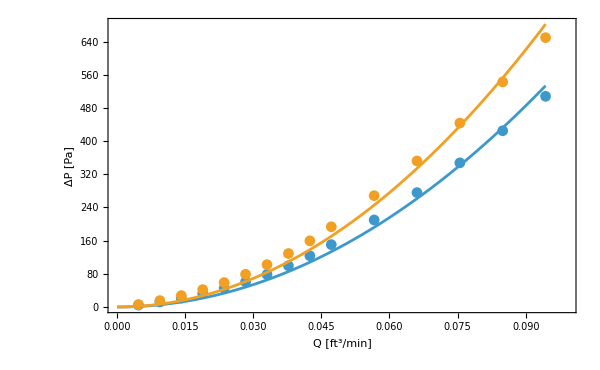

```mathematica
(*R2.1*)t={{10,4.484,5.86},{20,12.08,15.46},{30,21.4,27.55},{40,32.33,41.91},{50,45.26,58.91},{60,60.57,78.92},{70,78.48,102.1},{80,99.41,128.9},{90,123.5,159.5},{100,150.4,193.4},{120,209.8,268.4},{140,275.8,352},{160,347.5,443.4},{180,424.9,542.6},{200,507.9,649.4}};
t=Table[{0.00047194745t[[i,1]],t[[i,2]],t[[i,3]]},{i,1,Length[t]}];
a1=a/.FindFit[t[[All,{1,2}]],a x^2,a,x]
a2=a/.FindFit[t[[All,{1,3}]],a x^2,a,x]
Show[ListPlot[{t[[All,{1,2}]],t[[All,{1,3}]]},PlotRange->{{0,1.05t[[-1,1]]},{0,1.05t[[-1,3]]}},Joined->False,Mesh->All,Frame->True,ImageSize->600,FrameStyle->Directive[Black,18],FrameLabel->{"Q [ft^3/min]","ΔP [Pa]"}],Plot[{a1 x^2,a2 x^2},{x,0,t[[-1,1]]}]]
```